```mathematica
Get["/Users/tomeichlersmith/Desktop/Summer Research 2016/Necessary Functions.m"]
```

{pluck, peak, parametricregion, egsystem, QOtriangleApprox, QOtriangleApprox2, freqsintens, graphfi, keep, loudfreqs, graphweight, colorfreqs, freqband, freqlines, print3Dborder, print3Dregion, p}

## Investigation

### Square

```mathematica
squarex[t_]:=p[{{0,0},{1,0},{1,1},{0,1},{0,0}}][t][[1]]; (* 0≤ϵ<2 *)
squarey[t_]:=p[{{0,0},{1,0},{1,1},{0,1},{0,0}}][t][[2]];(* 0≤t≤4 *)
squarepara={{squarex,squarey},{0,4}};
squaregion=parametricregion[squarepara];
{squarevals,squarefuncs}=egsystem[20][squaregion];
gridpts[Num_]:=Flatten[N[Table[{i/(Num+1),j/(Num+1)},{i,Num},{j,Num}]],1];
```

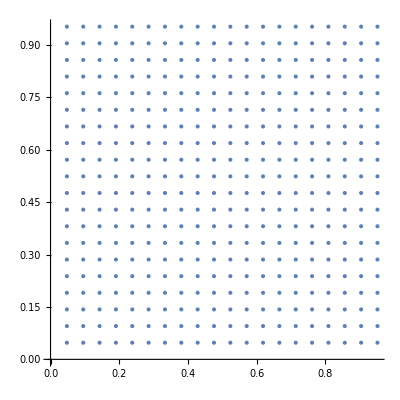

```mathematica
sgrid=gridpts[20];
ListPlot[sgrid,AspectRatio->Automatic]
```

```mathematica
(* WARNING: Really long calculation ~30min *)
Module[{squarethump},
squarethump[pt_]:=pluck[squarepara,75,pt];
SPluckVals=Table[(QOtriangleApprox2[squarethump[pt],squarefuncs])^2,{pt,sgrid}]];
```

```mathematica
(* WARNING: Really long calculation ~30min *)
Module[{squarethump},
squarethump[pt_]:=peak[squarepara,0.05,pt];
SPeakVals=Table[(QOtriangleApprox2[squarethump[pt],squarefuncs])^2,{pt,sgrid}]];
```

```mathematica
SPluckPlots=ListContourPlot[#,Frame->False]&/@Table[
Append[sgrid[[i]],SPluckVals[[i,j]]],{j,Length[SPluckVals[[1]]]},{i,Length[sgrid]}];
SPeakPlots=ListContourPlot[#,Frame->False]&/@Table[
Append[sgrid[[i]],SPeakVals[[i,j]]],{j,Length[SPeakVals[[1]]]},{i,Length[sgrid]}];
SNodalLines=Table[ContourPlot[ef[x,y]==0,{x,y}∈squaregion,ContourStyle->Red,Frame->False],{ef,squarefuncs}];
SquareCompare=Table[{Show[SPluckPlots[[i]],SNodalLines[[i]]],Show[SPeakPlots[[i]],SNodalLines[[i]]]},{i,Length[SNodalLines]}];
```

```mathematica
GraphicsGrid[{Table[Flatten[SquareCompare[[i;;i+3]],1],{i,{1,5,9,13,17}}]}]
```

```mathematica
Manipulate[SquareCompare[[i]],{i,1,Length[SquareCompare],1}]
```

### Circle

```mathematica
circlepara={{(Cos[#])&,(Sin[#])&},{0,2Pi}};
ciregion=parametricregion[circlepara];
{circlevals,circlefuncs}=egsystem[20][ciregion];
cgridpts[Num_]:=RandomPoint[ciregion,Num];
```

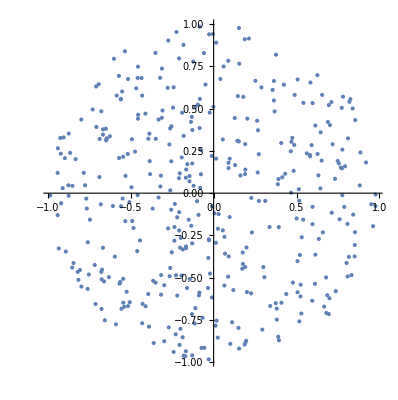

```mathematica
cgrid=cgridpts[400];
ListPlot[cgrid,AspectRatio->Automatic]
```

```mathematica
(* WARNING: Really long calculation ~15min *)
Module[{circlethump,intvals},
circlethump[pt_]:=pluck[circlepara,100,pt];
CPluckVals=Table[(QOtriangleApprox2[circlethump[point],circlefuncs])^2,{point,cgrid}]];
```

```mathematica
(* WARNING: Really long calculation ~15min *)
Module[{cthumps,intvals},
cthumps[pt_]:=peak[circlepara,0.05,pt];
CPeakVals=Table[(QOtriangleApprox2[cthumps[point],circlefuncs])^2,{point,cgrid}]];
```

```mathematica
CPluckPlots=ListContourPlot/@Table[
Append[cgrid[[i]],CPluckVals[[i,j]]],{j,Length[CPluckVals[[1]]]},{i,Length[cgrid]}];
CPeakPlots=ListContourPlot/@Table[
Append[cgrid[[i]],CPeakVals[[i,j]]],{j,Length[CPeakVals[[1]]]},{i,Length[cgrid]}];
CNodalLines=Table[ContourPlot[ef[x,y]==0,{x,y}∈ciregion,ContourStyle->Red],{ef,circlefuncs}];
CircleCompare=Table[{Show[CPluckPlots[[i]],CNodalLines[[i]]],Show[CPeakPlots[[i]],CNodalLines[[i]]]},{i,Length[CNodalLines]}];
```

```mathematica
GraphicsGrid[{Table[Flatten[CircleCompare[[i;;i+3]],1],{i,{1,5,9,13,17}}]}]
```

```mathematica
Manipulate[CircleCompare[[i]],{i,1,Length[CircleCompare],1}]
```

### Weird

```mathematica
weirdpara=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/Weird Shape.m"];
weirdregion=parametricregion[weirdpara];
{wfreqs,wfuncs}=egsystem[20][weirdregion];
wgridgen[Num_]:=RandomPoint[weirdregion,Num];
```

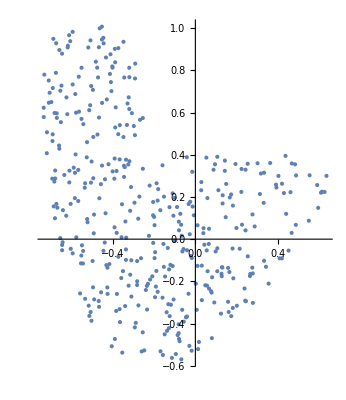

```mathematica
wgrid=wgridgen[400];
ListPlot[wgrid,AspectRatio->Automatic]
```

```mathematica
Module[{wpluck,wpeak},
wpluck[pt_]:=pluck[weirdpara,100,pt];
wpeak[pt_]:=peak[weirdpara,0.05,pt];
WPluckVals=Table[(QOtriangleApprox2[wpluck[pt],wfuncs])^2,{pt,wgrid}];
WPeakVals=Table[(QOtriangleApprox2[wpeak[pt],wfuncs])^2,{pt,wgrid}];]
```

```mathematica
WPluckPlots=ListContourPlot/@Table[
Append[wgrid[[i]],WPluckVals[[i,j]]],{j,Length[WPluckVals[[1]]]},{i,Length[wgrid]}];
WPeakPlots=ListContourPlot/@Table[
Append[wgrid[[i]],WPeakVals[[i,j]]],{j,Length[WPeakVals[[1]]]},{i,Length[wgrid]}];
WNodalLines=Table[ContourPlot[ef[x,y]==0,{x,y}∈weirdregion,ContourStyle->Red],{ef,wfuncs}];
WeirdCompare=Table[{Show[WPluckPlots[[i]],WNodalLines[[i]]],Show[WPeakPlots[[i]],WNodalLines[[i]]]},{i,20}];
```

```mathematica
Manipulate[WeirdCompare[[i]],{i,1,Length[WeirdCompare],1}]
```

The peak function seems to follow the nodal lines similar to what is expected, while the pluck seems to be almost unpredictable. This would make the process of finding thumping points that mute specific frequencies easier and faster when using the peak function as our model. Of course, this choice fully depends on what is realistic and/or possibly accepted in the scientific/acoustic field. It could be that neither of these ‘thump’ functions fully model what a realistic drum is like and therefore both would be equal approximations in that both would be equally far away from reality. Obviously, if prior research has shown one of these to be more correct or our measurements show one of these to be more correct, we can proceed with that option.